# PWBA

## Using Guassian Quadrature

```mathematica
mp = 938.2723;
amu=931.502;
m23F=21423.077578;
m25F =23294.116;
ℏ=197.3269788; (* MeV fm /c^2*)
ee=ℏ/137;
LGAUSS[Nr_]:=Module[{root,xi,DP,wg,x},
root= Sort[Solve[LegendreP[Nr, x] == 0, {x}] // N];
xi=x/.root;
DP=Evaluate[D[LegendreP[Nr,x],x]]/.root;
wg=2/((1-xi^2)DP^2);
Table[{xi[[i]],wg[[i]]},{i,1,Nr}]
]
GaussianIntegrate[f_Symbol,a_,b_,nGauss_]:=Module[
{func,xwlist,temp},
func[x_]:=f[x];
xwlist=Transpose[LGAUSS[nGauss]];
(*Print[ListPlot[Transpose[Join[{xwlist[[1]]},{func[(b-a)/2 xwlist[[1]]+(b+a)/2]}]]]];*)
(b-a)/2 Total[xwlist[[2]]func[(b-a)/2 xwlist[[1]]+(b+a)/2]];
(b-a)/2 Sum[xwlist[[2,i]]func[(b-a)/2 xwlist[[1,i]]+(b+a)/2],{i,1,nGauss}]

]
PWBA[U_Symbol,q_,nGauss_]:=Module[
{integral},
integral[r_]:=U[r] r Sin[q r]/q;
(mp/ℏ^2)^2 Power[GaussianIntegrate[integral,0,10,nGauss],2]
]
MEcm[A1_,A2_,T1Lab_]:=Module[
{P1,P2,Pc,β,γ,L,P1c,P2c,mμ},
P1={A1 amu+T1Lab,√((A1 amu+T1Lab)^2-(A1 amu)^2)};
P2={A2 amu,0};
Pc = (P1+P2)/2;
β=Pc[[2]]/Pc[[1]];
γ=1/(√(1-β^2));
L=γ{{1,-β},{-β,1}};
P1c=L.P1;
P2c=L.P2;
(*{mμ=(A1 A2)/(A1+A2),P1c[[1]]-A1 amu }*)
{mμ=(P1c[[1]]P2c[[1]])/(P1[[1]]+P2[[1]]),1/(2mμ)((P1c[[1]])^2-(A1 amu)^2)}

]
```

```mathematica
Solve[27==27]
```

```mathematica
Cot[0]//Simplify
```

ComplexInfinity

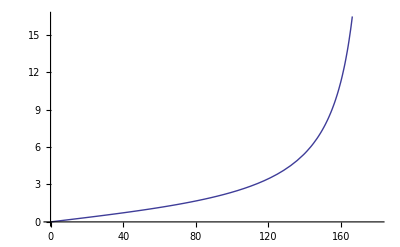

```mathematica
Plot[2 Tan[θ/2 Degree],{θ,0,180}]
```

```mathematica
Solve[{
1/2 m v0^2==1/2 m v^2 + eee/d,
v0 bb == v d
},{v,d}
]
```

{{v→(-eee-√(eee^2+bb^2 m^2 v0^4))/(bb m v0),d→(eee-√(eee^2+bb^2 m^2 v0^4))/(m v0^2)},{v→(-eee+√(eee^2+bb^2 m^2 v0^4))/(bb m v0),d→(eee+√(eee^2+bb^2 m^2 v0^4))/(m v0^2)}}

```mathematica
Remove[d,b,θ,a]
```

```mathematica
Simplify[Solve[(b/Sin[α])^2/(d-b/Sin[α])^2-1==Tan[α]^2,{b}],{d>0,Sin[θ/2]>0}]
```

{{b→d Cot[α/2]},{b→d Tan[α/2]}}

```mathematica
Tan[α]^2+1//Simplify
```

Sec[α]^2

```mathematica
Simplify[(Cos[α]+1)/Sin[α]]
```

Cot[α]+Csc[α]

```mathematica
Manipulate[
Plot[{2 82 1.44/(EE (1-(Cot[θ/2 Degree]))^2)},{EE,10,40},GridLines->Automatic],
{θ,10,180,10}]
```

## SandBox

120.267

13935.4

9.27815

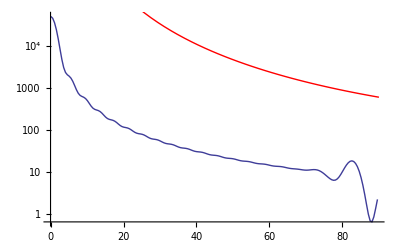

```mathematica
T=MEcm[16,208,130][[2]]
Mμ=MEcm[16,208,130][[1]]
k=(√(2 Mμ T))/ℏ
V0=-1;
R0=4;
pot[r_]:=(8 82 ee)/r^2 ;(*-1/(1+Exp[(r-2)/0.6]);*)(*Piecewise[{{V0,0≤ r<R0}},0];*)
dsc=Table[{θ,PWBA[pot,2 k Sin[(θ Degree)/2],30]},{θ,0.1,90,0.5 }];
Show[
ListLogPlot[dsc,Joined->True,PlotRange->All],
LogPlot[((8 82 ee)/(2 T))^2 10(1/Sin[(θ Degree)/2])^4,{θ,0,90},PlotStyle->Red]
(*LogPlot[((2 mp)/ℏ^2 V0/(2k Sin[(θ Degree)/2]))^2 R0^2 SphericalBesselJ[1,2k Sin[(θ Degree)/2] R0]^2,{θ,0,90},PlotStyle->Red]*)
]
```

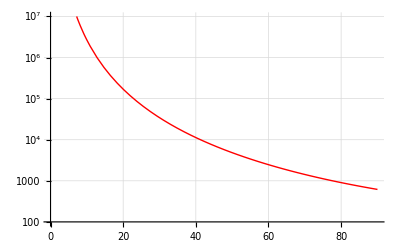

```mathematica
LogPlot[((8 82 ee)/(2T))^2 10(1/Sin[(θ Degree)/2])^4,{θ,0,90},PlotStyle->Red,PlotRange->{100,10^7},GridLines->Automatic]
```

## Old Integration method

3.732

1.6836

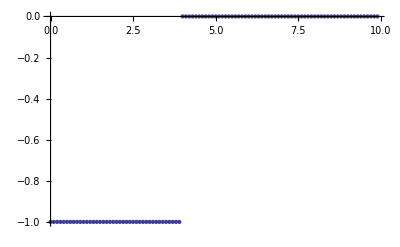

```mathematica
T=289;
n=100;
dr=0.1;
dθ=0.001;
V0=-1;
R0=4;
k=(√(2mp T))/ℏ(* fm^-1 *)
λ=2 π/k(* fm *)
DR=Table[r,{r,0,n dr,dr}];
Dθ=Table[θ,{θ,0.00001,π,dθ}];
Dq=Table[2 k Sin[Dθ[[i]]/2],{i,1,Length[Dθ]}];
Dtest=Table[Piecewise[{{V0,r<R0},{0,R0≤r }}],{r,0,n dr, dr}];
Dtest=Table[{DR[[i]],Dtest[[i]]},{i,1,n}];
ListPlot[Dtest]
PWBAIntegral[U_,r_,q_]:=U r Sin[q r]/q
w=Table[{Dθ[[p]] 180/π,Norm[(mp/ℏ^2) Sum[PWBAIntegral[Dtest[[i,2]],(DR[[i]]+DR[[i+1]])/2,Dq[[p]] ]dr,{i,1,n-1}]]^2},{p,1,Length[Dθ]}];
```

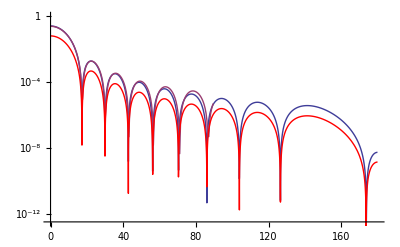

```mathematica
Show[
ListLogPlot[{w,dsc},Joined->True]
,LogPlot[((2 mp)/ℏ^2 V0/(2k Sin[(θ Degree)/2]))^2 R0^2 SphericalBesselJ[1,2k Sin[(θ Degree)/2] R0]^2,{θ,0,180},PlotStyle->Red]
]
```

```mathematica
k=4;
V0=-1;
R0=1;
f[x_,θ_]:=mp/ℏ^2 Piecewise[{{V0 x Sin[2k Sin[θ/2] x]/(2k Sin[θ/2]),x<R0},{0,R0≤x}}]
dx=0.015;
Rmax=3;
Dx=Table[x,{x,0,Rmax,dx}];
Dθ=Table[θ,{θ,0.0001,π,0.01}];
a=Table[{Dθ[[p]] 180/π,Sum[f[Dx[[i]],Dθ[[p]]]dx,{i,1,Length[Dx]-1}]^2},{p,1,Length[Dθ]}];
b=Table[{Dθ[[p]] 180/π,Sum[f[Dx[[i]],Dθ[[p]]]dx,{i,2,Length[Dx]}]^2},{p,1,Length[Dθ]}];
c=Table[{Dθ[[p]] 180/π,Sum[f[(Dx[[i]]+Dx[[i+1]])/2,Dθ[[p]]]dx,{i,1,Length[Dx]-1}]^2},{p,1,Length[Dθ]}];
t=Table[{Dθ[[p]] 180/π,NIntegrate[f[x,Dθ[[p]]],{x,0,Rmax}]^2},{p,1,Length[Dθ]}];
```

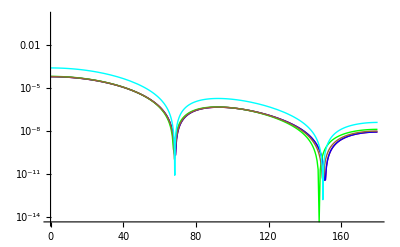

{θ→68.3436}

```mathematica
Show[
ListLogPlot[{a,b,c,t},Joined->True,PlotStyle->{Red,Blue,Green,Brown}],
LogPlot[((2 mp)/ℏ^2 1/(2k Sin[(θ Degree)/2]))^2 R0^2 SphericalBesselJ[1,2k Sin[(θ Degree)/2] R0]^2,{θ,0,180},PlotStyle->Cyan]
]
FindRoot[SphericalBesselJ[1,2k Sin[θ Degree/2] R0]==0,{θ,50}]
```

```mathematica
FunctionExpand[SphericalBesselJ[1,q x]]
```

-Cos[q x]/(q x)+Sin[q x]/(q^2 x^2)

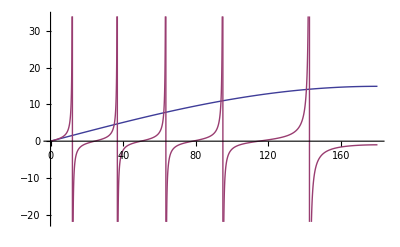

```mathematica
Plot[{2k Sin[θ/2 Degree] R0,Tan[2k Sin[θ/2 Degree] R0]},{θ,0,180}]
```